```mathematica
(*S x I ->S*)
```

```mathematica
{
}
```

{}

```mathematica
FullSimplify[
Normalize@{x,Sqrt[x]}.
Normalize@{x,Log[2,x]}
,x∈Reals]
```

(x (x^(3/2) Log[2]+Log[x]))/(√Abs[x] √(x (1+Abs[x]) (Abs[Log[x]]^2+x^2 Log[2]^2)))

```mathematica
FullSimplify[
Normalize@{x,Sqrt[x]}.
Normalize@{x,Log[2,x]}
,{x,Log[x]}∈Reals]
```

(x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x])))

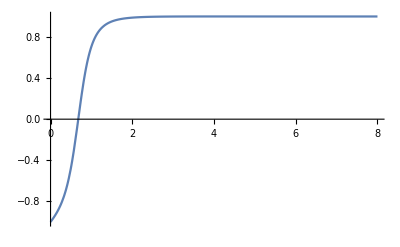

```mathematica
Plot[(x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x]))),{x,-8,8},PlotRange->{-1,1}]
```

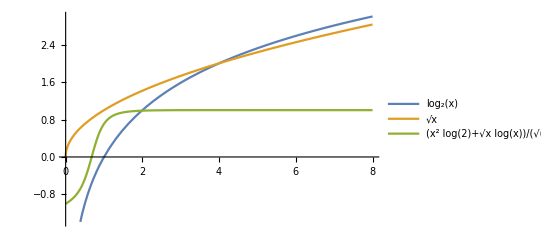

```mathematica
Plot[
{Log[2,x],Sqrt[x],(x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x])))}
,{x,0,8}
,PlotLegends->"Expressions"]
```

```mathematica
f[g[x]]==λ g[x]
```

f[g[x]]==λ g[x]

```mathematica
Reduce[f[g[x]]==λ g[x]]
```

(f[0]==0&&g[x]==0)||((Re[g[x]]<0||(Re[g[x]]==0&&(Im[g[x]]<0||Im[g[x]]>0))||Re[g[x]]>0)&&λ==f[g[x]]/g[x])

```mathematica
FullSimplify[f[g[x]]==λ g[x],{x,g[x],f[x],λ}∈Reals]
```

f[g[x]]==λ g[x]

```mathematica
FullSimplify[Reduce[f[g[x]]==λ g[x]],{x,g[x],f[x],λ}∈Reals]
```

(f[0]==0&&g[x]==0)||(g[x]≠0&&λ==f[g[x]]/g[x])

```mathematica
x
```

x

```mathematica
f[x]
```

f[x]

```mathematica
InverseFunction[f][x]
```

f^(-1)[x]

```mathematica
Composition[f,g,h]
```

f@*g@*h

```mathematica
InverseFunction@Composition[f,g,h]
```

h^(-1)@*g^(-1)@*f^(-1)

```mathematica
Composition[f,g,h][x]
```

f[g[h[x]]]

```mathematica
InverseFunction[Composition[f,g,h]][x]
```

h^(-1)[g^(-1)[f^(-1)[x]]]

```mathematica
Composition[
InverseFunction[Composition[f,g,h]],
Composition[f,g,h]][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction::ifun will be suppressed during this calculation.

x

```mathematica
Manipulate[
∫_0^a (x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x])))ⅆx,
{a,0,100}]
```

```mathematica
Manipulate[
∫_0^a (x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x])))ⅆx,
{a,0,100,1}]
```

```mathematica
1+2
```

3

```mathematica
∫_0^10 (x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x])))ⅆx
```

∫_0^10 (x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x])))ⅆx

```mathematica
NIntegrate[(x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x]))),{x,0,10}]
```

8.60251

```mathematica
With[{a=20},
NIntegrate[(x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x]))),{x,0,a}]/a
]
```

0.930114

```mathematica
Limit[(x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x]))),x->∞]
```

1

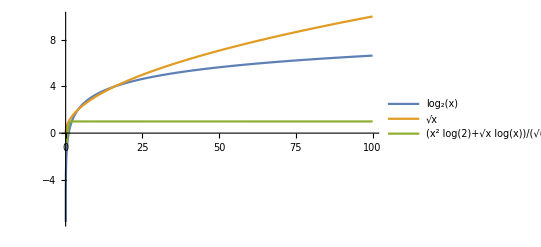

```mathematica
Plot[
{Log[2,x],Sqrt[x],(x^2 Log[2]+√x Log[x])/(√(x (x^2 Log[2]^2+Log[x]^2) (x+Sign[x])))}
,{x,0,100}
,PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[1==∫_0^a √(1+4 x^2)ⅆx,a∈Reals]
```

ConditionalExpression[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a≠0]

```mathematica
PositiveReals
```

```mathematica
FullSimplify[1==∫_0^a √(1+4 x^2)ⅆx,a∈]
```

2 a √(1+4 a^2)+ArcSinh[2 a]==4

```mathematica
FullSimplify[
Solve[1==∫_0^a √(1+4 x^2)ⅆx,a,]
,a∈]
```

{{a→Root0.764Root[{-4+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,0.76392666331709104116}]0.763926663317091}}

```mathematica
FullSimplify[
Solve[2==∫_0^a √(1+4 x^2)ⅆx,a,]
,a∈]
```

{{a→Root1.21Root[{-8+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,1.2144034265683531658}]1.2144034265683532}}

```mathematica
FullSimplify[
Solve[3==∫_0^a √(1+4 x^2)ⅆx,a,]
,a∈]
```

{{a→Root1.55Root[{-12+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,1.5540451904777992342}]1.5540451904777992}}

```mathematica
FullSimplify[
Integrate[√(1+4 x^2),x]
,a∈]
```

1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])

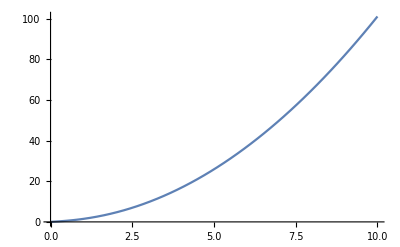

```mathematica
Plot[1/4 (2 x √(1+4 x^2)+ArcSinh[2 x]),{x,0,10}]
```

```mathematica
FullSimplify[
Solve[100==∫_0^a √(1+4 x^2)ⅆx,a,]
,a∈]
```

{{a→Root9.95Root[{-400+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,9.9475632997257427899}]9.947563299725743}}

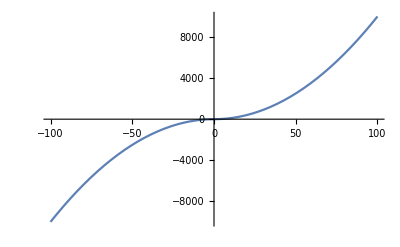

```mathematica
Plot[1/4 (2 x √(1+4 x^2)+ArcSinh[2 x]),{x,-100,100}]
```

```mathematica
FullSimplify[
Normalize@{x,1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])}.
Normalize@{x,x^2}
,x∈Reals]
```

(Abs[x] (4+2 x √(1+4 x^2)+ArcSinh[2 x]))/(√((1+x^2) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2)))

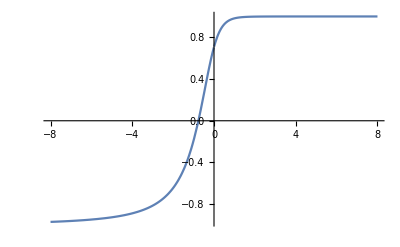

```mathematica
Plot[(Abs[x] (4+2 x √(1+4 x^2)+ArcSinh[2 x]))/(√((1+x^2) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2))),{x,-8,8}]
```

```mathematica
FullSimplify[
Normalize@{x,1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])}.
Normalize@{x,x^3}
,x∈Reals]
```

(Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2)))

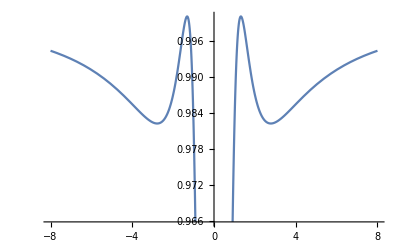

```mathematica
Plot[(Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2))),{x,-8,8}]
```

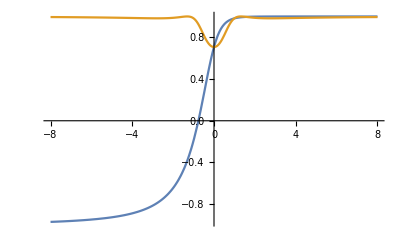

```mathematica
Plot[
{(Abs[x] (4+2 x √(1+4 x^2)+ArcSinh[2 x]))/(√((1+x^2) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2))),(Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2)))}
,{x,-8,8}]
```

```mathematica
1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])-((Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2)))x^3)
```

1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])-(x^3 Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2)))

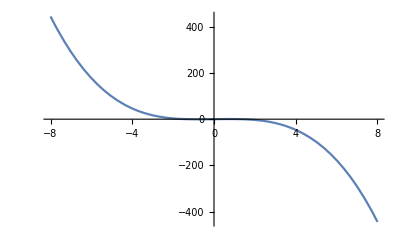

```mathematica
Plot[1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])-(x^3 Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2))),{x,-8,8}]
```

```mathematica
(x^3 Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2)))
```

(x^3 Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2)))

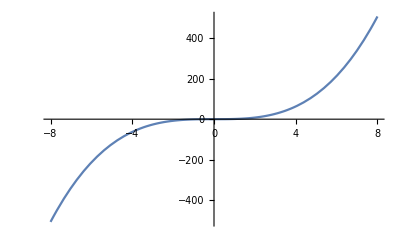

```mathematica
Plot[(x^3 Abs[x] (4+2 x^2 √(1+4 x^2)+x ArcSinh[2 x]))/(√((1+x^4) (16 x^2+(2 x √(1+4 x^2)+ArcSinh[2 x])^2))),{x,-8,8}]
```

```mathematica
FullSimplify[
Normalize@{x,2 x^3}.
Normalize@{x,x^3}
,x∈Reals]
```

(1+2 x^4)/(√(1+5 x^4+4 x^8))

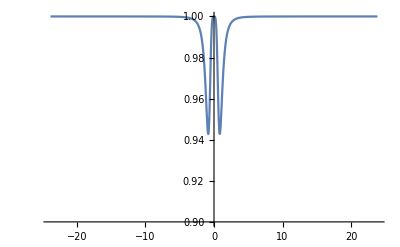

```mathematica
Plot[(1+2 x^4)/(√(1+5 x^4+4 x^8)),{x,-23.862222222222222,23.862222222222222},PlotRange->{0.9,1}]
```

```mathematica
(1+2 x^4)/(√(1+5 x^4+4 x^8))x^3
```

(x^3 (1+2 x^4))/(√(1+5 x^4+4 x^8))

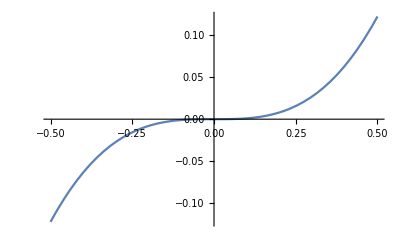

```mathematica
Plot[(x^3 (1+2 x^4))/(√(1+5 x^4+4 x^8)),{x,-1/2,1/2}]
```

```mathematica
FullSimplify[
Normalize@{x,2 x^3}.
Normalize@{x,x^3}
,x∈Reals]
```

(1+2 x^4)/(√(1+5 x^4+4 x^8))

```mathematica
2 x^3-(x^3 (1+2 x^4))/(√(1+5 x^4+4 x^8))
```

2 x^3-(x^3 (1+2 x^4))/(√(1+5 x^4+4 x^8))

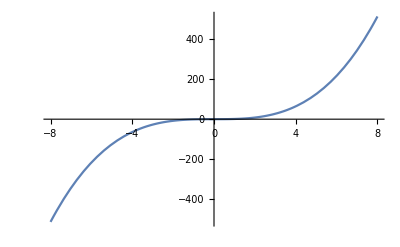

```mathematica
Plot[2 x^3-(x^3 (1+2 x^4))/(√(1+5 x^4+4 x^8)),{x,-8,8}]
```

```mathematica
(f[x]-a[x]g[x])+h[x]==0
```

f[x]-a[x] g[x]+h[x]==0

```mathematica
-Sin[x]==1-Sin[x]
```

-Sin[x]==1-Sin[x]

```mathematica
Reduce[-Sin[x]==1-Sin[x]]
```

False

```mathematica
(1+Cos[π θ])/2
```

1/2 (1+Cos[π θ])

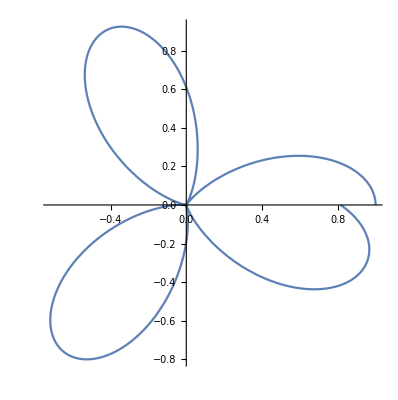

```mathematica
PolarPlot[1/2 (1+Cos[π θ]),{θ,0,2 π}]
```

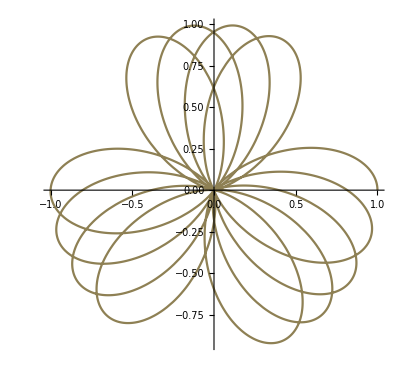

```mathematica
PolarPlot[
1/2 (1+Cos[π θ])
,{θ,0,8π}
,ColorFunction->"DarkRainbow",PlotLegends->"Expressions"]
```

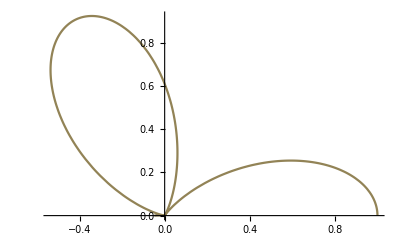

```mathematica
PolarPlot[
1/2 (1+Cos[π θ])
,{θ,0,π}
,ColorFunction->"DarkRainbow",PlotLegends->"Expressions"]
```

```mathematica
1/2 (1+Cos[π θ])==0
```

1/2 (1+Cos[π θ])==0

```mathematica
Reduce[1/2 (1+Cos[π θ])==0]
```

Cos[π θ]==-1

```mathematica
Solve[Cos[π θ]==-1,{θ}]
```

{{θ→ConditionalExpression[(-π+2 π C[1])/π,C[1]∈ℤ]},{θ→ConditionalExpression[(π+2 π C[1])/π,C[1]∈ℤ]}}

```mathematica
1/2 (1+Cos[π θ])/.θ->(π+2 π)/π
```

0

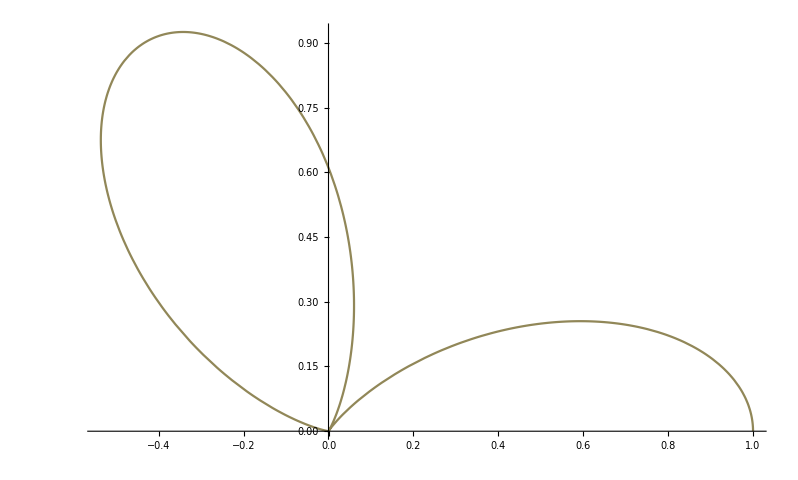

```mathematica
PolarPlot[
1/2 (1+Cos[π θ])
,{θ,0,(π+2 π)/π}
,ColorFunction->"DarkRainbow",PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[
Normalize@{x,f[x]}.
Normalize@{x,g[x]}
,{x,f[x],g[x]}∈Reals]
```

(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))

```mathematica
FullSimplify[
Normalize@{x,x}.
Normalize@{x,g[x]}
,{x,f[x],g[x]}∈Reals]
```

((x+g[x]) Sign[x])/(√2 √(x^2+g[x]^2))

```mathematica
FullSimplify[
Normalize@{x,f[x]}.
Normalize@{x,g[x]}
,{x,f[x],g[x]}∈Reals]
```

(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))

```mathematica
FullSimplify[
Normalize@{x,f[x]}.
Normalize@{x,f[x]}
,{x,f[x],g[x]}∈Reals]
```

1

```mathematica
FullSimplify[
Normalize@{x,f[x]}.
Normalize@{x,g[x]}
,{x,f[x],g[x]}∈Reals]
```

(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))

```mathematica
Sum[10^i,{i,1,10}]
```

11111111110

```mathematica
Sum[10^-i,{i,1,10}]
```

1111111111/10000000000

```mathematica
N[1111111111/10000000000]
```

0.111111

```mathematica
Sum[9^-i,{i,1,10}]
```

435848050/3486784401

```mathematica
Sum[9 10^-i,{i,1,10}]
```

9999999999/10000000000

```mathematica
N[9999999999/10000000000]
```

1.

```mathematica
1-lim_(n->∞) (∑_(i=1))^n 9 10^-i≥0
```

```mathematica
With[{f=Identity,g=Function[x,2x]},
(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))
]
```

(3 x^2)/(√10 √(x^4))

```mathematica
Plot[(3 x^2)/(√10 √(x^4)),{x,-1,1}]
```

-Graphics-

```mathematica
√(^(x^2))
```

√(Null^(x^2))

```mathematica
√(x^2)
```

√(x^2)

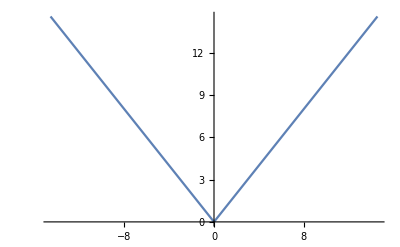

```mathematica
Plot[√(x^2),{x,-14.56,14.56}]
```

```mathematica
D[√(x^2),x]
```

x/(√(x^2))

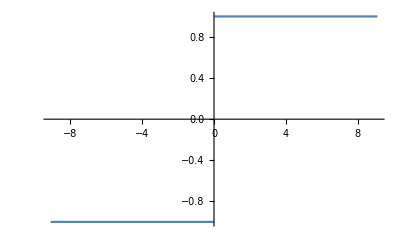

```mathematica
Plot[x/(√(x^2)),{x,-9.100000000000001,9.100000000000001}]
```

```mathematica
√((x+1)^2)
```

√((1+x)^2)

```mathematica
(x+1)^2
```

(1+x)^2

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
√((1+x)^2)-1+2 x
```

-1+2 x+√((1+x)^2)

```mathematica
√((1+x)^2)-(1+2 x)
```

-1-2 x+√((1+x)^2)

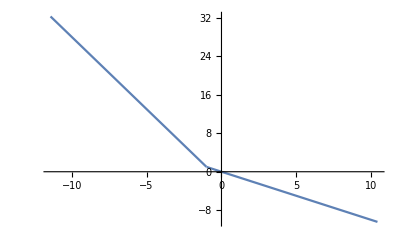

```mathematica
Plot[-1-2 x+√((1+x)^2),{x,-11.42,10.42}]
```

```mathematica
√((1+x)^2)-(1+2 x+x^2/2)
```

-1-2 x-x^2/2+√((1+x)^2)

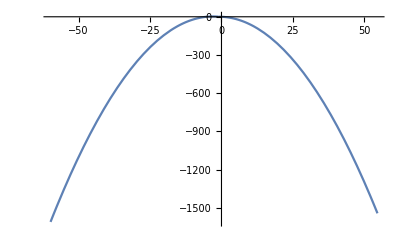

```mathematica
Plot[-1-2 x-x^2/2+√((1+x)^2),{x,-59.7958963030476,54.55982832554781}]
```

```mathematica
FullSimplify[-1-2 x-x^2/2+√((1+x)^2)]
```

-1+√((1+x)^2)-1/2 x (4+x)

```mathematica
SurfaceData["TorisphericalDome","Properties"]
```

{algebraic degree,algebraic equation,alternate names,area element,associated people,Cartesian equation,centroid of solid,Christoffel symbol of the second kind,(map) chromatic number,classes,cross sections,entity classes,Euler characteristic,filled region,coefficients of the first fundamental form,Gaussian curvature,generalized diameter,genus,3-D graphics,image,implicit Gaussian curvature,implicit mean curvature,implicit normal vector,moment of inertia tensor of solid,CDF of lengths,mean line segment length,PDF of lengths,mean curvature,metric tensor,name,number of nodes,normal vector,parameters,parametric equations,principal curvatures,number of punctures,related Wolfram Language symbols,Ricci tensor,Riemann tensor,coefficients of the second fundamental form,semialgebraic description,singular points,sport objects,surface area,variable constraints,variable descriptions,variables,vector length,volume of solid}

```mathematica
SurfaceData["TorisphericalDome",EntityProperty["Surface","Graphics3D"]]
```

-Graphics3D-

```mathematica
Plot3D[
√(1-x^2-y^2)
,{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Laplacian[√(1-x^2-y^2),{x,y}]
```

-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))

```mathematica
Plot3D[
-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))
,{x,y}∈Disk[]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
J[{a_,b_}]:={-b,a}
```

```mathematica
Grad[√(1-x^2-y^2),{x,y}]
```

{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}

```mathematica
Solve[{-x/(√(1-x^2-y^2))==0,-y/(√(1-x^2-y^2))==0},{x,y}]
```

{{x→0,y→0}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

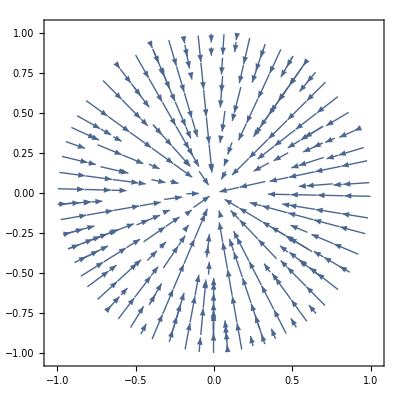

```mathematica
StreamPlot[
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}
,{x,y}∈Disk[]]
```

```mathematica
Div[√(1-x^2-y^2),{x,y}]
```

Div::sclr: The scalar expression √(1-x^2-y^2) does not have a divergence.

√(1-x^2-y^2){x,y}

```mathematica
Curl[√(1-x^2-y^2),{x,y}]
```

{y/(√(1-x^2-y^2)),-x/(√(1-x^2-y^2))}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

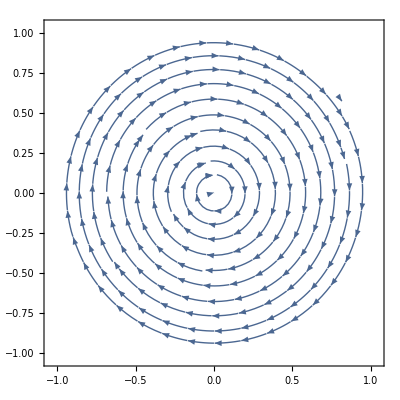

```mathematica
StreamPlot[
{y/(√(1-x^2-y^2)),-x/(√(1-x^2-y^2))}
,{x,y}∈Disk[]]
```

```mathematica
With[{f=Identity,g=Function[x,2x]},
f[x]+g[x](x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))
]
```

x+(3 √(2/5) x^3)/(√(x^4))

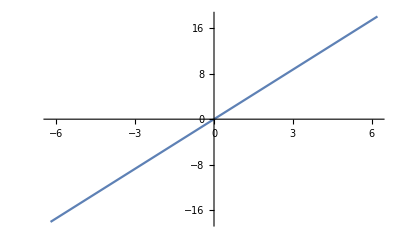

```mathematica
Plot[x+(3 √(2/5) x^3)/(√(x^4)),{x,-6.222176477399997,6.222176477399997}]
```

```mathematica
With[{f=Identity,g=Function[x,2x]},
f[x]-g[x](x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))
]
```

x-(3 √(2/5) x^3)/(√(x^4))

```mathematica
FullSimplify[x-(3 √(2/5) x^3)/(√(x^4))]
```

x-(3 √(2/5) √(x^4))/x

```mathematica
FullSimplify[x-(3 √(2/5) x^3)/(√(x^4))]
```

```mathematica
With[{f=Identity,g=Function[x,2x]},
FullSimplify[f[x]-g[x](x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2))),Element[x|f[x]|g[x],Reals]]
]
```

x-3 √(2/5) x

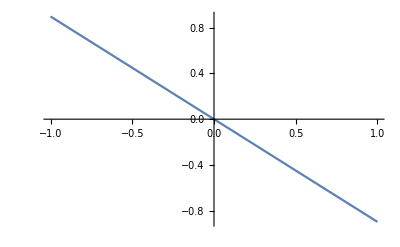

```mathematica
Plot[x-3 √(2/5) x,{x,-1,1}]
```

```mathematica
With[{f=Identity,g=Function[x,2x]},
FullSimplify[f[x]+g[x](x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2))),Element[x|f[x]|g[x],Reals]]
]
```

x+3 √(2/5) x

```mathematica
With[{f=Identity,g=Function[x,2x]},
FullSimplify[f[x]g[x](x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2))),Element[x|f[x]|g[x],Reals]]
]
```

3 √(2/5) x^2

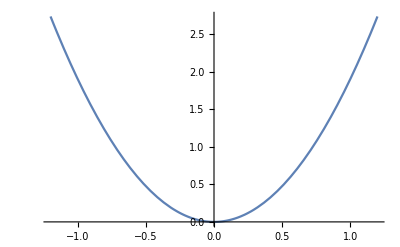

```mathematica
Plot[3 √(2/5) x^2,{x,-1.2,1.2}]
```

```mathematica
2x x
```

2 x^2

```mathematica
N@3 √(2/5)
```

1.89737

```mathematica
With[{f=Identity,g=Function[x,2x]},
FullSimplify[(f[x]+g[x])(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2))),Element[x|f[x]|g[x],Reals]]
]
```

(9 x)/(√10)

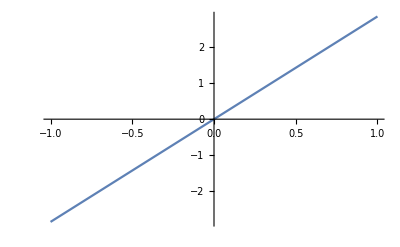

```mathematica
Plot[(9 x)/(√10),{x,-1,1}]
```

```mathematica
x+2x
```

3 x

```mathematica
N@(9/(√10))
```

2.84605

```mathematica
(f[x+α]-f[x])/α
```

(-f[x]+f[x+α])/α

```mathematica
Exp[f'[x]/f[x]]
```

ⅇ^(f'[x]/f[x])

```mathematica
With[{f=Function[x,x^2]},
Exp[f'[x]/f[x]]
]
```

ⅇ^(2/x)

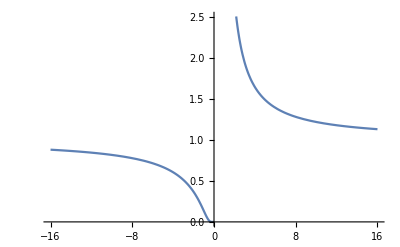

```mathematica
Plot[ⅇ^(2/x),{x,-16,16}]
```

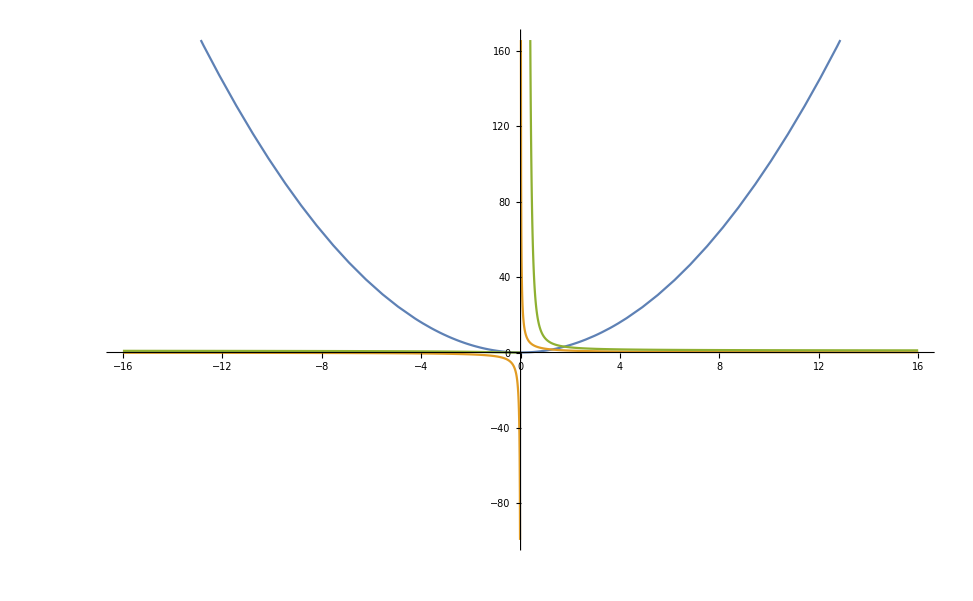

```mathematica
Plot[
{x^2,2/x,ⅇ^(2/x)}
,{x,-16,16}]
```

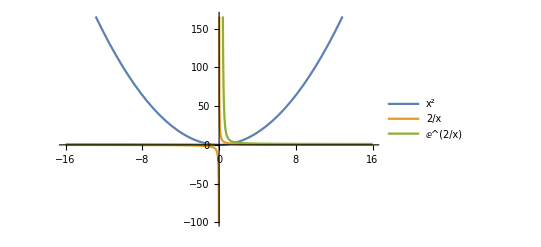

```mathematica
Plot[
{x^2,2/x,ⅇ^(2/x)}
,{x,-16,16}
,PlotLegends->"Expressions"]
```

```mathematica
(f[x]-f[x-α])/α
```

(f[x]-f[x-α])/α

```mathematica
Limit[(f[x]-f[x-α])/α,α->0]
```

lim_(α→0) (f[x]-f[x-α])/α

```mathematica
Limit[(f[x]-f[x-α])/α,α->0]==Limit[(f[x-α]-f[x])/α,α->0]
```

lim_(α→0) (f[x]-f[x-α])/α==lim_(α→0) (-f[x]+f[x-α])/α

```mathematica
Reduce[lim_(α->0) (f[x]-f[x-α])/α==lim_(α->0) (-f[x]+f[x-α])/α]
```

lim_(α→0) (f[x]-f[x-α])/α==lim_(α→0) (-f[x]+f[x-α])/α

```mathematica
FindInstance[lim_(α->0) (f[x]-f[x-α])/α==lim_(α->0) (-f[x]+f[x-α])/α,{x,α}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[lim_(α→0) (f[x]-f[x-α])/α==lim_(α→0) (-f[x]+f[x-α])/α,{x,α}]

```mathematica
Limit[(f[x]-f[x-α])/α,α->0]==Limit[(f[x+α]-f[x])/α,α->0]
```

lim_(α→0) (f[x]-f[x-α])/α==lim_(α→0) (-f[x]+f[x+α])/α

```mathematica
Reduce[lim_(α->0) (f[x]-f[x-α])/α==lim_(α->0) (-f[x]+f[x+α])/α]
```

lim_(α→0) (f[x]-f[x-α])/α==lim_(α→0) (-f[x]+f[x+α])/α

```mathematica
FindInstance[lim_(α->0) (f[x]-f[x-α])/α==lim_(α->0) (-f[x]+f[x+α])/α,{x,α}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[lim_(α→0) (f[x]-f[x-α])/α==lim_(α→0) (-f[x]+f[x+α])/α,{x,α}]

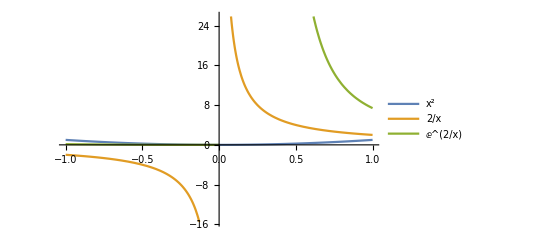

```mathematica
Plot[
{x^2,2/x,ⅇ^(2/x)}
,{x,-1,1}
,PlotLegends->"Expressions"]
```

```mathematica
D[Exp[f'[x]/f[x]],x]
```

ⅇ^(f'[x]/f[x]) (-f'[x]^2/f[x]^2+f''[x]/f[x])

```mathematica
Simplify[ⅇ^(f'[x]/f[x]) (-f'[x]^2/f[x]^2+f''[x]/f[x])]
```

(ⅇ^(f'[x]/f[x]) (-f'[x]^2+f[x] f''[x]))/f[x]^2

```mathematica
f''[x]f'[x]==f[x]
```

f'[x] f''[x]==f[x]

```mathematica
DSolve[f'[x] f''[x]==f[x],{f[x],f[x]},{x}]
```

{{f[x]→InverseFunction[-((-2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]]},{f[x]→InverseFunction[((2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]]},{f[x]→InverseFunction[((-1)^(2/3) (2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]]}}

```mathematica
f[x]/.%151
```

{InverseFunction[-((-2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]],InverseFunction[((2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]],InverseFunction[((-1)^(2/3) (2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]]}

```mathematica
InverseFunction[((2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]]
```

InverseFunction[((2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&][x+C[2]]

```mathematica
(((2/3)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-#1^2/(2 C[1])] #1 (1+#1^2/(2 C[1]))^(1/3))/((2 C[1]+#1^2)^(1/3))&)[x]
```

((2/3)^(1/3) x (1+x^2/(2 C[1]))^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-x^2/(2 C[1])])/((x^2+2 C[1])^(1/3))

```mathematica
((2/3)^(1/3) x (1+x^2/(2 C[1]))^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-x^2/(2 C[1])])/((x^2+2 C[1])^(1/3))/.{C[1]->1}
```

((2/3)^(1/3) x (1+x^2/2)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-x^2/2])/((2+x^2)^(1/3))

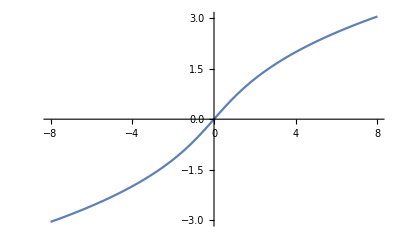

```mathematica
Plot[((2/3)^(1/3) x (1+x^2/2)^(1/3) Hypergeometric2F1[1/3,1/2,3/2,-x^2/2])/((2+x^2)^(1/3)),{x,-8,8}]
```

```mathematica
(1+Cos[π θ])/2
```

1/2 (1+Cos[π θ])

```mathematica
With[{a=Function[θ,(1+Cos[π θ])/2]},
(1-a[x])p+a q
]
```

p (1+1/2 (-1-Cos[π x]))+q Function[θ,1/2 (1+Cos[π θ])]

```mathematica
With[{a=Function[θ,(1+Cos[π θ])/2]},
(1-a[x])p+a[x] q
]
```

p (1+1/2 (-1-Cos[π x]))+1/2 q (1+Cos[π x])

```mathematica
With[{a=Function[θ,(1+Cos[π θ])/2],p=Identity,q=Function[x,x^2]},
(1-a[x])p[x]+a[x] q[x]
]
```

x (1+1/2 (-1-Cos[π x]))+1/2 x^2 (1+Cos[π x])

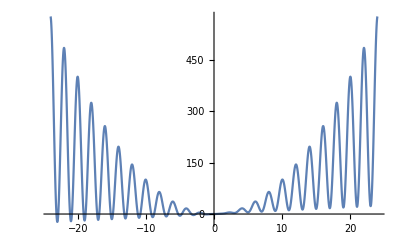

```mathematica
Plot[x (1+1/2 (-1-Cos[π x]))+1/2 x^2 (1+Cos[π x]),{x,-24.,24.}]
```

```mathematica
f[x,y]==g[x][y]
```

f[x,y]==g[x][y]

```mathematica
FindInstance[f[x,y]==g[x][y],{x,y}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[f[x,y]==g[x][y],{x,y}]

```mathematica
Laplacian[f[x,y],{x,y}]==λ f[x,y]
```

f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y]

```mathematica
DSolve[Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]
```

DSolve[f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]

```mathematica
DSolve[Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==λ f[x,y],f[x,y],{x,y}]
```

DSolve[f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y],f[x,y],{x,y}]

```mathematica
Solve[Laplacian[f[x,y],{x,y}]==λ f[x,y],λ]
```

{{λ→(f^(0,2)[x,y]+f^(2,0)[x,y])/f[x,y]}}

```mathematica
Exp[Laplacian[f[x],{x}]/f[x]]
```

ⅇ^(f''[x]/f[x])

```mathematica
D[f[g[x]],x]==f[D[g[x],x]]
```

f'[g[x]] g'[x]==f[g'[x]]

```mathematica
DSolve[f'[g[x]] g'[x]==f[g'[x]],{f[g[x]],g[x]},{x}]
```

DSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in f[g[x]] should literally match the independent variables.

DSolve[f'[g[x]] g'[x]==f[g'[x]],{f[g[x]],g[x]},{x}]

```mathematica
Exp[f'[x]/f[x]]
```

ⅇ^(f'[x]/f[x])

```mathematica
D[Exp[f'[x]/f[x]],x]
```

ⅇ^(f'[x]/f[x]) (-f'[x]^2/f[x]^2+f''[x]/f[x])

```mathematica
D[f'[x]/f[x],x]
```

-f'[x]^2/f[x]^2+f''[x]/f[x]

```mathematica
D[Exp[f[x]],{x,n}]==Exp[f[x]]D[f[x],{x,n}]
```

∂_{x,n} ⅇ^f[x]==ⅇ^f[x] f^(n)[x]

```mathematica
FullSimplify[
D[Exp[f[x]],{x,n}]==Exp[f[x]]D[f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈]
```

∂_{x,n} ⅇ^f[x]==ⅇ^f[x] f^(n)[x]

```mathematica
PositiveIntegers
```

```mathematica
FullSimplify[
D[Exp[f[x]],{x,n}]==Exp[f[x]]D[f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈]
```

```mathematica
D[f[x],{x,1}]
```

f'[x]

```mathematica
D[f[x],{x,0}]
```

f[x]

```mathematica
D[f[x],{x,0}]==Identity[f[x]]==f[x]
```

True

```mathematica
FullSimplify[
D[Exp[f[x]],{x,n}]==Exp[f[x]]D[f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
```

∂_{x,n} ⅇ^f[x]==ⅇ^f[x] f^(n)[x]

```mathematica
FullSimplify[
D[Exp[f'[x]/f[x]],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
```

∂_{x,n} ⅇ^(f'[x]/f[x])

```mathematica
FullForm[D[ⅇ^f[x], {x,n}]==ⅇ^f[x] Derivative[n][f][x]]
```

Equal[D[Power[E,f[x]],List[x,n]],Times[Power[E,f[x]],Derivative[n][f][x]]]

```mathematica
FullSimplify[
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
```

∂_{x,n} ⅇ^(f'[x]/f[x])==ⅇ^(f'[x]/f[x]) Binomial[n,K[1]] ∂_{x,K[1]} 1/f[x] ∂_{x,n-K[1]} f'[x]K[1]0n

```mathematica
Binomial[α,β]
```

Binomial[α,β]

```mathematica
DiscretePlot3D[Binomial[α,β],{α,1,20},{β,1,20}]
```

-Graphics3D-

```mathematica
Activate[D[ⅇ^(f'[x]/f[x]), {x,n}]==ⅇ^(f'[x]/f[x]) Binomial[n,K[1]] D[1/f[x], {x,K[1]}] D[f'[x], {x,n-K[1]}]K[1]0n]
```

∂_{x,n} ⅇ^(f'[x]/f[x])==ⅇ^(f'[x]/f[x]) ∑_(K[1]=0)^n Binomial[n,K[1]] ∂_{x,K[1]} 1/f[x] ∂_{x,n-K[1]} f'[x]

```mathematica
ⅇ^(f'[x]/f[x])∑_(K[1]=0)^n Binomial[n,K[1]] D[1/f[x], {x,K[1]}] D[f'[x], {x,n-K[1]}]
```

```mathematica
D[f[x]g[x],x]
```

g[x] f'[x]+f[x] g'[x]

```mathematica
Integrate[g[x] f'[x]+f[x] g'[x],x]
```

f[x] g[x]

```mathematica
Mean@LevyDistribution[μ,σ]
```

∞

```mathematica
FullForm[∞]
```

DirectedInfinity[1]

```mathematica
PDF[LevyDistribution[μ,σ],x]
```

Piecewise[{{(ⅇ^(-σ/(2 (x-μ))) (σ/(x-μ))^(3/2))/(√(2 π) σ), x>μ}, {0, True}}]

```mathematica
Manipulate[Plot[Piecewise[{{(ⅇ^(-σ/(2 (x-μ))) (σ/(x-μ))^(3/2))/(√(2 π) σ),x>μ}},0],{x,-8,8}],{μ,-8,8},{σ,-2,2}]
```

```mathematica
f[x-1]/f[x]
```

f[-1+x]/f[x]

```mathematica
D[f[-1+x]/f[x], x]
```

f'[-1+x]/f[x]-(f[-1+x] f'[x])/f[x]^2

```mathematica
Simplify[f'[-1+x]/f[x]-(f[-1+x] f'[x])/f[x]^2]
```

(f[x] f'[-1+x]-f[-1+x] f'[x])/f[x]^2

```mathematica
With[{},
FullSimplify[
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
]
```

∂_{x,n} ⅇ^(f'[x]/f[x])==ⅇ^(f'[x]/f[x]) Binomial[n,K[1]] ∂_{x,K[1]} 1/f[x] ∂_{x,n-K[1]} f'[x]K[1]0n

```mathematica
With[{n=1,f=Identity},
FullSimplify[
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
]
```

True

```mathematica
With[{n=1},
FullSimplify[
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
]
```

True

```mathematica
With[{f=Identity},
FullSimplify[
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
]
```

DifferenceRoot[Function[{y,n},{n y[n]+(1+2 x+2 n x) y[1+n]+(2+n) x^2 y[2+n]==0,y[0]==ⅇ^(1/x),y[1]==-ⅇ^(1/x)/x^2}]][n]==(-1)^n ⅇ^(1/x) x^(-1-n)

```mathematica
With[{f=Identity},
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
]
```

n! DifferenceRoot[Function[{y,n},{n y[n]+(1+2 x+2 n x) y[1+n]+(2+n) x^2 y[2+n]==0,y[0]==ⅇ^(1/x),y[1]==-ⅇ^(1/x)/x^2}]][n]==ⅇ^(1/x) x^(-1-n) FactorialPower[-1,n]

```mathematica
With[{f=Exp},
FullSimplify[
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
,{x,f[x]}∈Reals∧n∈
]
]
```

True

```mathematica
Identity[x]^2
```

x^2

```mathematica
FullForm@(Identity[x]^2)
```

Power[x,2]

```mathematica
With[{f=Exp},
D[Exp[f'[x]/f[x]],{x,n}]==Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]
]
```

True

```mathematica
D[Exp[f'[x]/f[x]],{x,n}]/.{f->Exp}
```

0

```mathematica
Exp[f'[x]/f[x]]D[f'[x]/f[x],{x,n}]/.{f->Exp}
```

ⅇ (-1)^K[1] ⅇ^-x Binomial[n,K[1]] ∂_{x,n-K[1]} ⅇ^xK[1]0n

```mathematica
Activate[ⅇ (-1)^K[1] ⅇ^-x Binomial[n,K[1]] D[ⅇ^x, {x,n-K[1]}]K[1]0n]
```

ⅇ ∑_(K[1]=0)^n (-1)^K[1] ⅇ^-x Binomial[n,K[1]] ∂_{x,n-K[1]} ⅇ^x

```mathematica
FullForm[ⅇ ∑_(K[1]=0)^n (-1)^K[1] ⅇ^-x Binomial[n,K[1]] D[ⅇ^x, {x,n-K[1]}]]
```

Times[E,Sum[Times[Power[-1,K[1]],Power[E,Times[-1,x]],Binomial[n,K[1]],D[Power[E,x],List[x,Plus[n,Times[-1,K[1]]]]]],List[K[1],0,n]]]

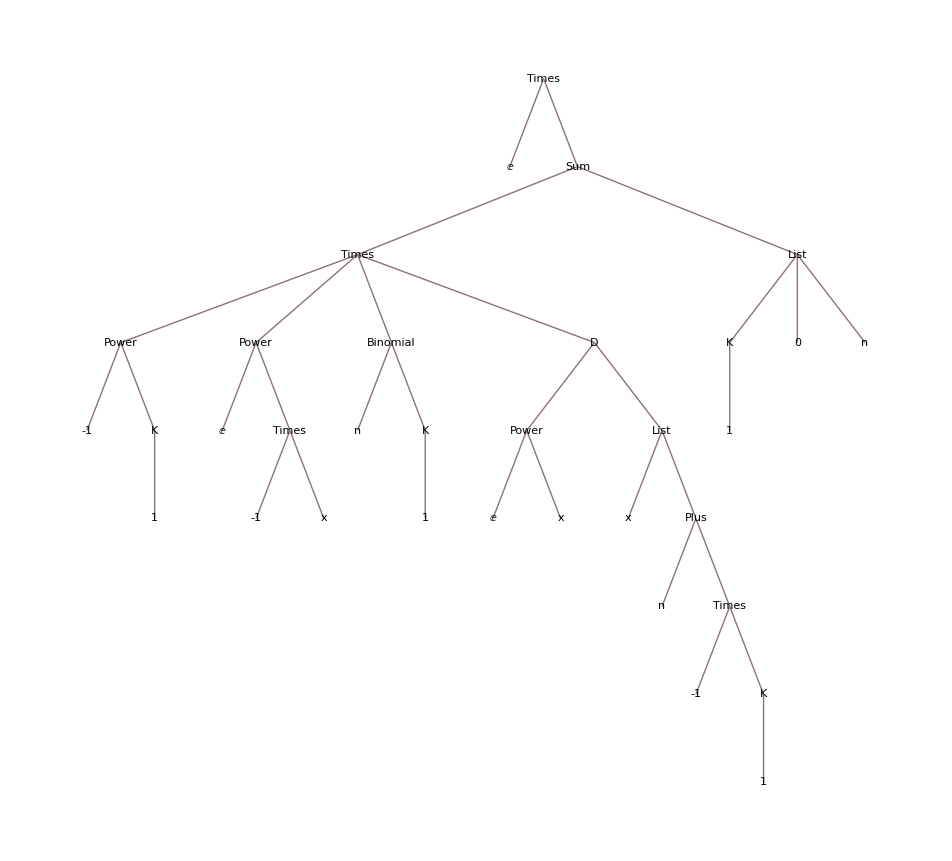

```mathematica
TreeForm[ⅇ ∑_(K[1]=0)^n (-1)^K[1] ⅇ^-x Binomial[n,K[1]] D[ⅇ^x, {x,n-K[1]}]]
```

```mathematica
ⅇ ∑_(K[1]=0)^n (-1)^K[1] ⅇ^-x Binomial[n,K[1]] D[ⅇ^x, {x,n-K[1]}]/.K[1]->i
```

ⅇ ∑_(i=0)^n (-1)^i ⅇ^-x Binomial[n,i] ∂_{x,-i+n} ⅇ^x

```mathematica
ⅇ ∑_(i=0)^n Binomial[n,i]
```

2^n ⅇ

```mathematica
∑_(i=0)^n Binomial[n,i]
```

2^n

```mathematica
ⅇ ∑_(i=0)^n (-1)^i ⅇ^-x Binomial[n,i]
```

ⅇ^(1-x) n

```mathematica
D[Exp[x],{x,n}]
```

ⅇ^x

```mathematica
∑_(i=0)^n (-1)^i ⅇ^-x Binomial[n,i]
```

ⅇ^-x n

```mathematica
1
```

0

```mathematica
KroneckerDelta[x]
```

x

```mathematica
ZTransform[x,x,z]
```

1

```mathematica
FourierSequenceTransform[x,x,ω]
```

1

```mathematica
Table[x,{x,1,20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
∑_(x=1)^∞ x
```

0

```mathematica
Table[x,{x,1,20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FourierTransform[Exp[-t^2] Sin[t],t,ω]
```

(ⅈ (-1+Cosh[ω]+Sinh[ω]) (Cosh[1/4 (1+ω)^2]-Sinh[1/4 (1+ω)^2]))/(2 √2)

```mathematica
FourierTransform[Sin[t],t,ω]
```

ⅈ √(π/2) DiracDelta[-1+ω]-ⅈ √(π/2) DiracDelta[1+ω]

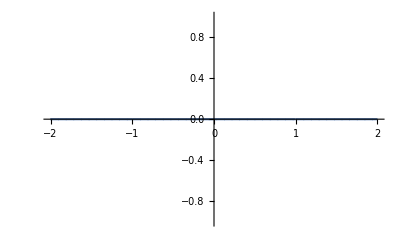

```mathematica
ReImPlot[
ⅈ √(π/2) DiracDelta[-1+ω]-ⅈ √(π/2) DiracDelta[1+ω]
,{ω,-2,2}]
```

```mathematica
FourierTransform[Sin[2t],t,ω]
```

ⅈ √(π/2) DiracDelta[-2+ω]-ⅈ √(π/2) DiracDelta[2+ω]

```mathematica
FourierTransform[Cos[t]Sin[2t],t,ω]
```

1/2 ⅈ √(π/2) DiracDelta[-3+ω]+1/2 ⅈ √(π/2) DiracDelta[-1+ω]-1/2 ⅈ √(π/2) DiracDelta[1+ω]-1/2 ⅈ √(π/2) DiracDelta[3+ω]

```mathematica
Together[1/2 ⅈ √(π/2) DiracDelta[-3+ω]+1/2 ⅈ √(π/2) DiracDelta[-1+ω]-1/2 ⅈ √(π/2) DiracDelta[1+ω]-1/2 ⅈ √(π/2) DiracDelta[3+ω]]
```

1/4 ⅈ (√(2 π) DiracDelta[-3+ω]+√(2 π) DiracDelta[-1+ω]-√(2 π) DiracDelta[1+ω]-√(2 π) DiracDelta[3+ω])

```mathematica
ⅇ ∑_(i=0)^n (-1)^i ⅇ^-x Binomial[n,i] D[ⅇ^x, {x,-i+n}]
```

ⅇ ∑_(i=0)^n (-1)^i ⅇ^-x Binomial[n,i] ∂_{x,-i+n} ⅇ^x

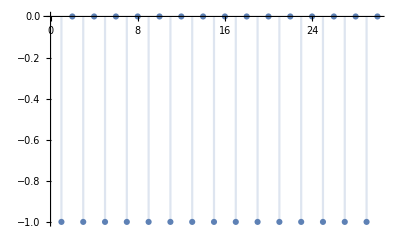

```mathematica
DiscretePlot[
Sum[(-1)^i,{i,1,a}],{a,1,30,1}]
```

```mathematica
ComplexPlot[z,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[z^2,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[Sqrt@z,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
(ⅇ) ∑_(i=0)^n ((-1)^i) (ⅇ^-x) (Binomial[n,i])( D[ⅇ^x, {x,-i+n}])
```

ⅇ ∑_(i=0)^n (-1)^i ⅇ^-x Binomial[n,i] ∂_{x,-i+n} ⅇ^x

```mathematica
ⅇ ∑_(i=0)^n (-1)^i ⅇ^-x Binomial[n,i]Exp[x]
```

ⅇ n

```mathematica
Table[ⅇ n,{n,1,20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
∑_(n=1)^∞ ⅇ n
```

0

```mathematica
Table[n,{n,1,20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[n,{n,0,20,1}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Information[Plus]
```

```mathematica
SystemInformation[Plus]
```

SystemInformation[Plus]

```mathematica
WolframLanguageData[Plus]
```

Missing[UnknownEntity,{WolframLanguageSymbol,Plus}]

```mathematica
f[a,b]
```

f[a,b]

```mathematica
SetAttributes[f,Orderless]
```

```mathematica
f[a,b]
```

f[a,b]

```mathematica
f[a,f[b,c]]==f[a,b,c]
```

f[a,f[b,c]]==f[a,b,c]

```mathematica
SetAttributes[f,Flatten]
```

```mathematica
f[a,f[b,c]]==f[a,b,c]
```

f[a,f[b,c]]==f[a,b,c]

```mathematica
Attributes[f]
```

{Orderless}

```mathematica
SetAttributes[f,Flat]
```

```mathematica
Attributes[f]
```

{Flat,Orderless}

```mathematica
f[a,f[b,c]]==f[a,b,c]
```

True

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
f[f[x]]
```

f[x]

```mathematica
Attributes[1]
```

Attributes[1]

```mathematica
MemoryInUse[]
```

415094504

```mathematica
?f
```

```mathematica
?π
```

Missing[UnknownSymbol,π]

```mathematica
FullSimplify[
Normalize@{x,x f[x]}
,x∈Reals]
```

{x/(√(x^2+Abs[x f[x]]^2)),(x f[x])/(√(x^2+Abs[x f[x]]^2))}

```mathematica
FullSimplify[
Normalize@{x,x f[x]}
,{x,f[x]}∈Reals]
```

{x/(√(x^2 (1+f[x]^2))),(f[x] Sign[x])/(√(1+f[x]^2))}

```mathematica
{x/(√(x^2 (1+f[x]^2))),(f[x] Sign[x])/(√(1+f[x]^2))}/.f->Exp
```

{x/(√((1+ⅇ^(2 x)) x^2)),(ⅇ^x Sign[x])/(√(1+ⅇ^(2 x)))}

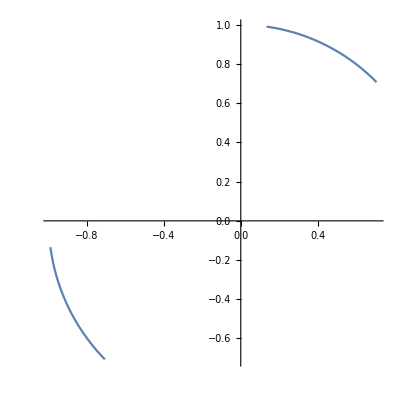

```mathematica
ParametricPlot[
{x/(√((1+ⅇ^(2 x)) x^2)),(ⅇ^x Sign[x])/(√(1+ⅇ^(2 x)))}
,{x,-2,2}]
```

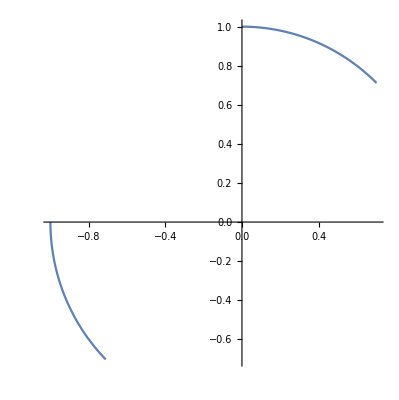

```mathematica
ParametricPlot[
{x/(√((1+ⅇ^(2 x)) x^2)),(ⅇ^x Sign[x])/(√(1+ⅇ^(2 x)))}
,{x,-20,20}]
```

```mathematica
Normalize@{x,x}
```

{x/(√2 Abs[x]),x/(√2 Abs[x])}

```mathematica
FullSimplify[Normalize@{x,x},x∈Reals]
```

{Sign[x]/(√2),Sign[x]/(√2)}

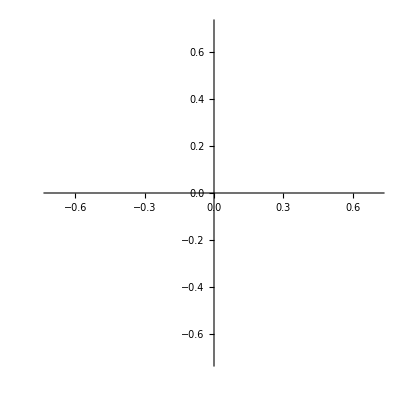

```mathematica
ParametricPlot[
{Sign[x]/(√2),Sign[x]/(√2)}
,{x,-20,20}]
```

```mathematica
FullSimplify[
Normalize@{x,x^2}
,x∈Reals]
```

{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}

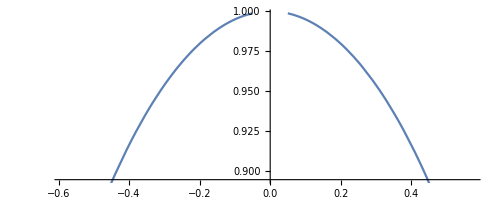

```mathematica
ParametricPlot[
{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}
,{x,-20,20}]
```

```mathematica
x==x/(√(x^2+x^4))
```

x==x/(√(x^2+x^4))

```mathematica
Solve[x==x/(√(x^2+x^4)),{x}]
```

{{x→-√(1/2 (-1+√5))},{x→√(1/2 (-1+√5))},{x→-ⅈ √(1/2 (1+√5))},{x→ⅈ √(1/2 (1+√5))}}

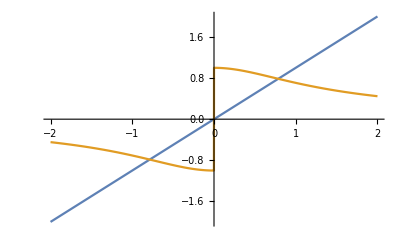

```mathematica
Plot[
{x,x/(√(x^2+x^4))}
,{x,-2,2}]
```

```mathematica
√(1/2 (-1+√5))
```

√(1/2 (-1+√5))

```mathematica
N[√(1/2 (-1+√5))]
```

0.786151

```mathematica
ContourPlot[x==x/(√(x^2+x^4)),{x,-2,2}]
```

ContourPlot[x==x/(√(x^2+x^4)),{x,-2,2}]

```mathematica
FullSimplify[
Normalize@{x,Exp[x]}
,x∈Reals]
```

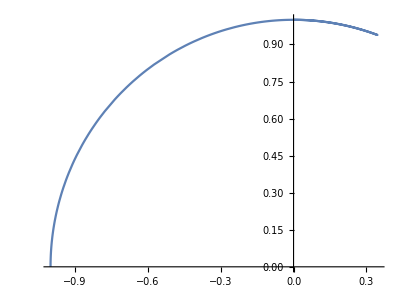

```mathematica
ParametricPlot[
{x/(√(ⅇ^(2 x)+x^2)),ⅇ^x/(√(ⅇ^(2 x)+x^2))}
,{x,-20,20}]
```

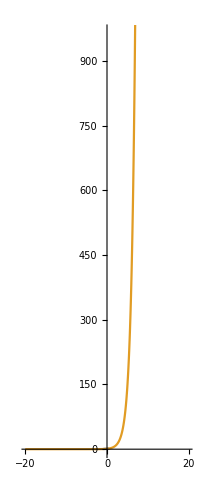

```mathematica
ParametricPlot[{
{x/(√(ⅇ^(2 x)+x^2)),ⅇ^x/(√(ⅇ^(2 x)+x^2))},
{x,Exp[x]}
},{x,-20,20}]
```

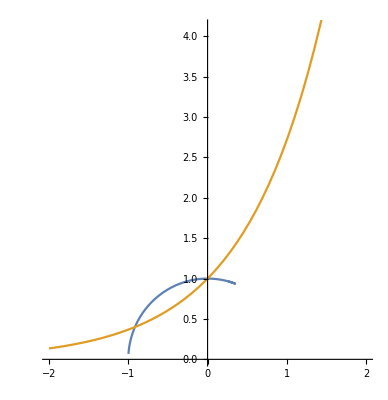

```mathematica
ParametricPlot[{
{x/(√(ⅇ^(2 x)+x^2)),ⅇ^x/(√(ⅇ^(2 x)+x^2))},
{x,Exp[x]}
},{x,-2,2}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x/(√(ⅇ^(2 x)+x^2)),ⅇ^x/(√(ⅇ^(2 x)+x^2))},
{x,Exp[x]}
},{x,-2,-2+a},PlotRange->{-2,2}],
{a,.01,10}]
```

```mathematica
Exp[x]10==x
```

10 ⅇ^x==x

```mathematica
Reduce[10 ⅇ^x==x]
```

C[1]∈ℤ&&x==-ProductLog[C[1],-10]

```mathematica
FindInstance[10 ⅇ^x==x,{x}]
```

{{x→-ProductLog[-24,-10]}}

```mathematica
ProductLog[x]
```

ProductLog[x]

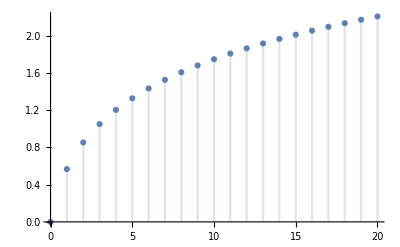

```mathematica
DiscretePlot[ProductLog[x],{x,0,20}]
```

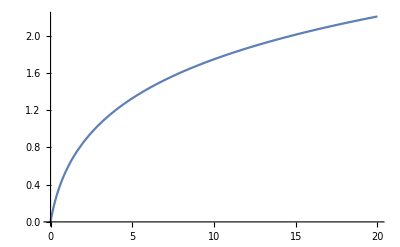

```mathematica
Plot[ProductLog[x],{x,0,20}]
```

```mathematica
FullSimplify[
Normalize@{x,ProductLog[x]}.
Normalize@{x,Log[x]}
,x∈Reals]
```

(x^2+Log[x] ProductLog[x])/(√((x^2+Abs[Log[x]]^2) (x^2+Abs[ProductLog[x]]^2)))

```mathematica
FullSimplify[
Normalize@{x,ProductLog[x]}.
Normalize@{x,Log[x]}
,{x,Log[x],ProductLog[x]}∈Reals]
```

(x^2+Log[x] ProductLog[x])/(√((x^2+Log[x]^2) (x^2+ProductLog[x]^2)))

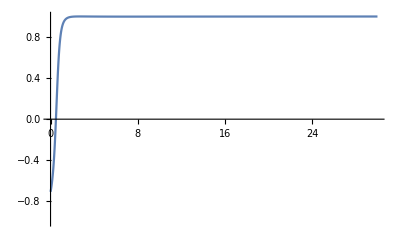

```mathematica
Plot[
(x^2+Log[x] ProductLog[x])/(√((x^2+Log[x]^2) (x^2+ProductLog[x]^2)))
,{x,0,30},PlotRange->{-1,1}]
```

```mathematica
Sinc[x]
```

Sinc[x]

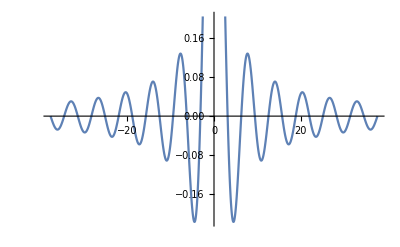

```mathematica
Plot[Sinc[x],{x,-37.69911184307752,37.69911184307752}]
```

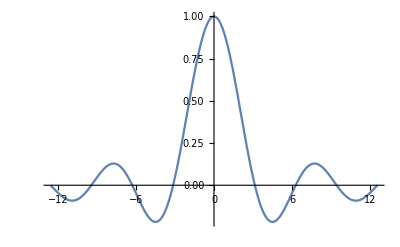

```mathematica
Plot[Sinc[x],{x,-4π,4π}]
```

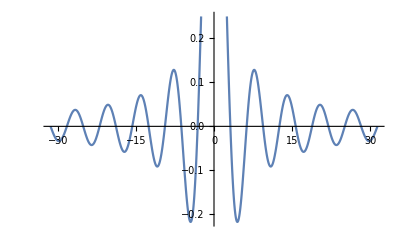

```mathematica
Plot[Sinc[x],{x,-10π,10π}]
```

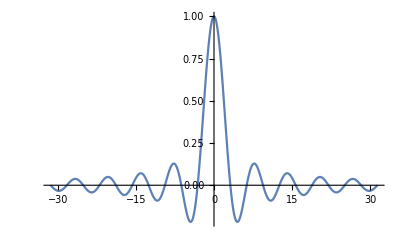

```mathematica
Plot[Sinc[x],{x,-10π,10π},PlotRange->Full]
```

```mathematica
FunctionExpand[Sinc[x]]
```

Sin[x]/x

```mathematica
Sin[x]/x
```

Sin[x]/x

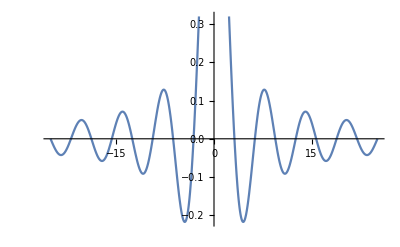

```mathematica
Plot[Sin[x]/x,{x,-25.132741228718345,25.132741228718345}]
```

```mathematica
D[Sinc[x],{x,2}]/Norm[{1,Sinc'[x]}]^3
```

(-(2 Cos[x])/x^2+(2 Sin[x])/x^3-Sin[x]/x)/((1+Abs[Cos[x]/x-Sin[x]/x^2]^2)^(3/2))

```mathematica
FullSimplify[(-(2 Cos[x])/x^2+(2 Sin[x])/x^3-Sin[x]/x)/((1+Abs[Cos[x]/x-Sin[x]/x^2]^2)^(3/2))]
```

(-2 x Cos[x]-(-2+x^2) Sin[x])/(x^3 (1+Abs[(x Cos[x]-Sin[x])/x^2]^2)^(3/2))

```mathematica
FullSimplify[D[Sinc[x],{x,2}]/Norm[{1,Sinc'[x]}]^3,x∈Reals]
```

-(x^3 (2 x Cos[x]+(-2+x^2) Sin[x]))/((x^4+(-x Cos[x]+Sin[x])^2)^(3/2))

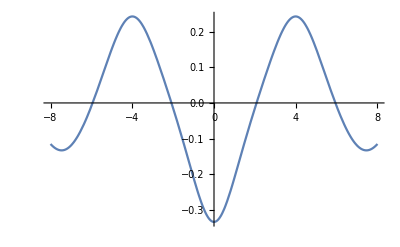

```mathematica
Plot[-(x^3 (2 x Cos[x]+(-2+x^2) Sin[x]))/((x^4+(-x Cos[x]+Sin[x])^2)^(3/2)),{x,-8,8}]
```

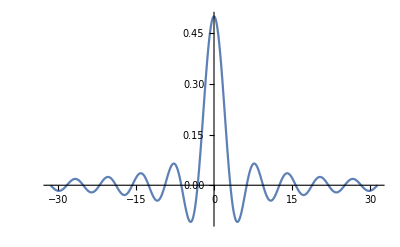

```mathematica
Plot[Sinc[x]/2,{x,-10π,10π},PlotRange->Full]
```

```mathematica
Sinc[x]/α==Cos[x]
```

Sinc[x]/α==Cos[x]

```mathematica
Reduce[Sinc[x]/α==Cos[x]]
```

(Sinc[x]==0&&Cos[x]==0&&α≠0)||(Cos[x]≠0&&α==Sec[x] Sinc[x]&&Sinc[x]≠0)

```mathematica
FindMinimum[Sinc[x],{x,0}]
```

{1.,{x→0.}}

```mathematica
FindMinimum[Sinc[x],{x,2}]
```

{-0.0579718,{x→17.2208}}

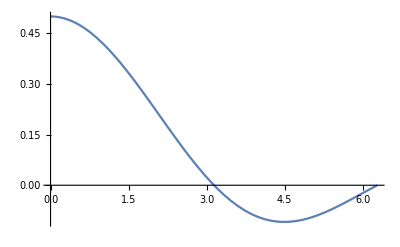

```mathematica
Plot[Sinc[x]/2,{x,0,2π},PlotRange->Full]
```

```mathematica
FindMinimum[Sinc[x],{x,4}]
```

{-0.217234,{x→4.49341}}

```mathematica
α π==4.493409457446784
```

π α==4.49341

```mathematica
Solve[π α==4.493409457446784,{α}]
```

{{α→1.4303}}

```mathematica
First@FindMinimum[Sinc[x],{x,4}]
```

-0.217234

```mathematica
Abs@First@FindMinimum[Sinc[x],{x,4}]+Sinc[0]
```

1.21723

```mathematica
FullSimplify[Reduce[(Abs@First@FindMinimum[Sinc[x],{x,4}]+Sinc[0])/α==1,α,Reals],α∈Reals]
```

α==1.21723

```mathematica
FindInstance[α==1.2172336282112217,{α}]
```

{{α→1.21723}}

```mathematica
(Abs@First@FindMinimum[Sinc[x],{x,4}]+Sinc[0])Sinc[x]
```

1.21723 Sinc[x]

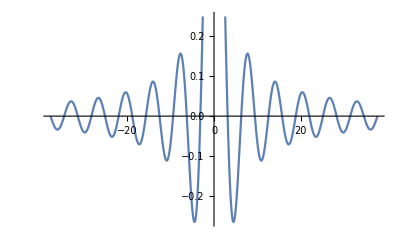

```mathematica
Plot[1.2172336282112217 Sinc[x],{x,-37.69911184307752,37.69911184307752}]
```

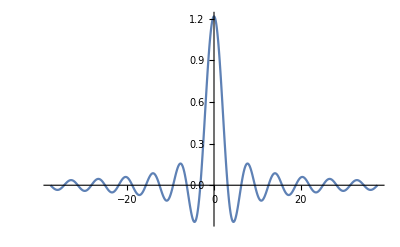

```mathematica
Plot[1.2172336282112217 Sinc[x],{x,-37.69911184307752,37.69911184307752},PlotRange->Full]
```

```mathematica
Sinc[x]/(Abs@First@FindMinimum[Sinc[x],{x,4}]+Sinc[0])
```

0.821535 Sinc[x]

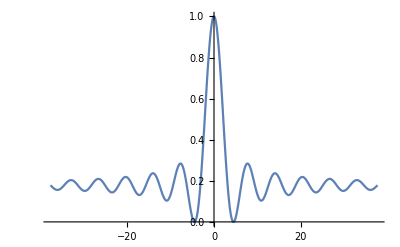

```mathematica
Plot[0.8215349763788107 Sinc[x]+(1-0.8215349763788107),{x,-37.69911184307752,37.69911184307752},PlotRange->Full]
```

```mathematica
a Sinc[x]+(1-a)
```

1-a+a Sinc[x]

```mathematica
Manipulate[Plot[1-a+a Sinc[x],{x,-10.,10.}],{a,-6.,6.}]
```

```mathematica
1-a+a Sinc[x]==1
```

1-a+a Sinc[x]==1

```mathematica
Solve[1-a+a Sinc[x]==1,{x}]
```

{{x→0}}

```mathematica
Reduce[1-a+a Sinc[x]==1]
```

a==0||Sinc[x]==1

```mathematica
(0.8215349763788107 Sinc[x]+(1-0.8215349763788107))+x
```

0.178465+x+0.821535 Sinc[x]

```mathematica
(0.8215349763788107 Sinc[x]+(1-0.8215349763788107))x
```

x (0.178465+0.821535 Sinc[x])

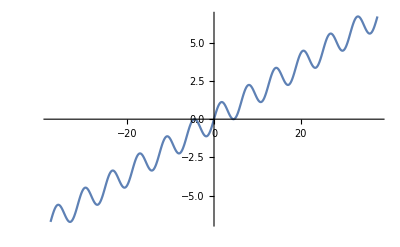

```mathematica
Plot[x (0.17846502362118932+0.8215349763788107 Sinc[x]),{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
(1-a)f[x]+a f[x]
```

(1-a) f[x]+a f[x]

```mathematica
Simplify[(1-a) f[x]+a f[x]]
```

f[x]

```mathematica
x (0.17846502362118932+0.8215349763788107 Sinc[x])+(1-( (0.17846502362118932+0.8215349763788107 Sinc[x])))x
```

x (0.821535-0.821535 Sinc[x])+x (0.178465+0.821535 Sinc[x])

```mathematica
Simplify[x (0.8215349763788107-0.8215349763788107 Sinc[x])+x (0.17846502362118932+0.8215349763788107 Sinc[x])]
```

0.+1. x

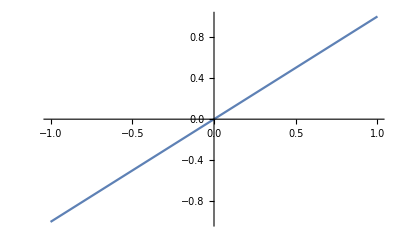

```mathematica
Plot[0.+1. x,{x,-1,1}]
```

```mathematica
Dt[x f[x],x]
```

f[x]+x f'[x]

```mathematica
Dt[x f[x]]
```

Dt[x] f[x]+x Dt[x] f'[x]

```mathematica
Dt[x f[x]]/.Dt[x]->1
```

f[x]+x f'[x]

```mathematica
x x
```

x^2

```mathematica
Manipulate[
Plot[
{x,x^2,(1-a)x+a x^2}
,{x,-2,2}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[
{x,x^2,(1-a)x+a x^2}
,{x,-2,2},PlotLegends->"Expressions"]
,{a,0,1}]
```

```mathematica
Laplacian[(1-a)x+a x^2,{x,a}]
```

2 a

```mathematica
Laplacian[(1-a)x+a x^2,{a,x}]
```

2 a

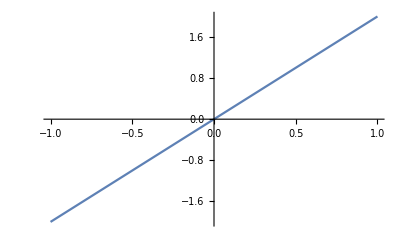

```mathematica
Plot[2 a,{a,-1,1}]
```

```mathematica
Plot3D[
(1-a)x+a x^2
,{x,-2,2},{a,0,1}]
```

-Graphics3D-

```mathematica
Integrate[(1-a)+a x^2,{x,-2,2}]
```

4 (1-a)+(16 a)/3

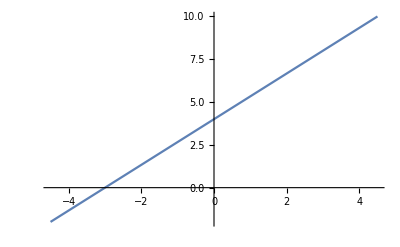

```mathematica
Plot[4 (1-a)+(16 a)/3,{a,-4.5,4.5}]
```

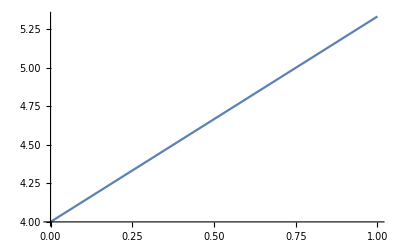

```mathematica
Plot[4 (1-a)+(16 a)/3,{a,0,1}]
```

```mathematica
(1-a)+a x^2/.a->0==(1-a)+a x^2/.a->1
```

1-(0==x^2)+x^2 (0==x^2)

```mathematica
Simplify[1-(0==x^2)+x^2 (0==x^2)]
```

1+(-1+x^2) (x==0)

```mathematica
((1-a)+a x^2/.a->0)==((1-a)+a x^2/.a->1)
```

1==x^2

```mathematica
((1-a)x+a x^2/.a->0)==((1-a)x+a x^2/.a->1)
```

x==x^2

```mathematica
Reduce[x==x^2]
```

x==0||x==1

```mathematica
((1-a)x+a x^2/.a->0)==((1-a)x+a x^2/.a->1)==(D[(1-a)x+a x^2,x]/.a->0)==(D[(1-a)x+a x^2,x]/.a->1)
```

x==x^2==1==2 x

```mathematica
Reduce[x==x^2==1==2 x]
```

False

```mathematica
(D[(1-a)x+a x^2,x]/.a->0)==(D[(1-a)x+a x^2,x]/.a->1)
```

1==2 x

```mathematica
Reduce[1==2 x]
```

x==1/2

```mathematica
f[x]+∫_0^α f'[x]ⅆx
```

f[x]+∫_0^α f'[x]ⅆx

```mathematica
f[x]+f[α]
```

f[x]+f[α]

```mathematica
With[{f=Identity},
FullSimplify[f[x]+f[α],{x,α}∈Reals]
]
```

x+α

```mathematica
With[{f=Sin},
FullSimplify[f[x]+f[α],{x,α}∈Reals]
]
```

Sin[x]+Sin[α]

```mathematica
Manipulate[Plot[Sin[x]+Sin[α],{x,-16.026018182541534,16.0260033916069}],{α,-16.026018182541534,16.0260033916069}]
```

```mathematica
f[x+a]==f[x]+f[a]
```

f[a+x]==f[a]+f[x]

```mathematica
Reduce[f[a+x]==f[a]+f[x]]
```

f[a]==-f[x]+f[a+x]

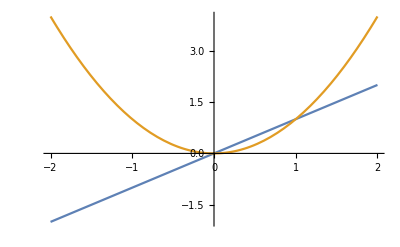

```mathematica
Plot[
{x,x^2}
,{x,-2,2}]
```

```mathematica
x^2-x
```

-x+x^2

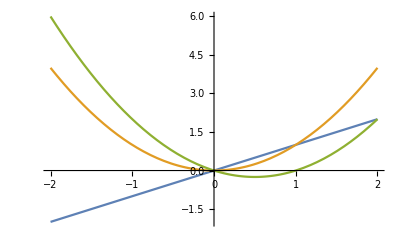

```mathematica
Plot[
{x,x^2,-x+x^2}
,{x,-2,2}]
```

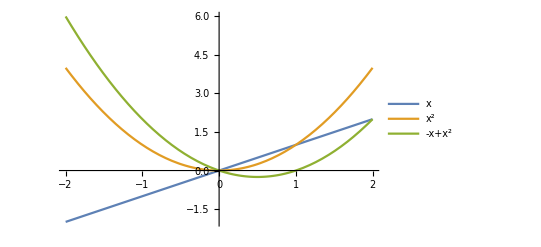

```mathematica
Plot[
{x,x^2,-x+x^2}
,{x,-2,2}
,PlotLegends->"Expressions"]
```

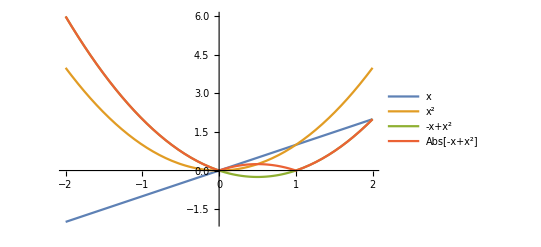

```mathematica
Plot[
{x,x^2,-x+x^2,Abs[-x+x^2]}
,{x,-2,2}
,PlotLegends->"Expressions"]
```

```mathematica
Reduce[-x+x^2≠Abs[-x+x^2],x,Reals]
```

0<x<1

```mathematica
Reduce[-x+x^2<0,x,Reals]
```

0<x<1

```mathematica
FullSimplify[(1-a[x])f[x]+a[x]g[x],{x,a[x],f[x],g[x]}∈Reals]
```

f[x]-a[x] f[x]+a[x] g[x]

```mathematica
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
```

(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))

```mathematica
FullSimplify[
(Normalize[{x,f[x]}].
Normalize[{x,g[x]}])f[x]+
-(Normalize[{x,f[x]}].
Normalize[{x,g[x]}])g[x]
,{x,f[x],g[x]}∈Reals]
```

((f[x]-g[x]) (x^2+f[x] g[x]))/(√((x^2+f[x]^2) (x^2+g[x]^2)))

```mathematica
FullSimplify[
(1-a[x])f[x]+a[x]g[x]
,{x,a[x],f[x],g[x]}∈Reals]
```

f[x]-a[x] f[x]+a[x] g[x]

```mathematica
FullSimplify[
((1-a[x])f[x]+a[x]g[x])g[x]
,{x,a[x],f[x],g[x]}∈Reals]
```

g[x] (f[x]-a[x] f[x]+a[x] g[x])

```mathematica
FullSimplify[
((1-a[x])f[x]+a[x]g[x])g[x]==a[x]
,{x,a[x],f[x],g[x]}∈Reals]
```

g[x] (f[x]-a[x] f[x]+a[x] g[x])==a[x]

```mathematica
Reduce[g[x] (f[x]-a[x] f[x]+a[x] g[x])==a[x]]
```

((g[x]==-1||g[x]==1)&&f[x]==0)||(-1-f[x] g[x]+g[x]^2≠0&&a[x]==-(f[x] g[x])/(-1-f[x] g[x]+g[x]^2))

```mathematica
FullSimplify[
Reduce[((1-a[x])f[x]+a[x]g[x])g[x]==a[x]]
,{x,a[x],f[x],g[x]}∈Reals∧-1-f[x] g[x]+g[x]^2≠0]
```

a[x]+(-1+a[x]) f[x] g[x]==a[x] g[x]^2

```mathematica
Reduce[a[x]+(-1+a[x]) f[x] g[x]==a[x] g[x]^2]
```

((g[x]==-1||g[x]==1)&&f[x]==0)||(-1-f[x] g[x]+g[x]^2≠0&&a[x]==-(f[x] g[x])/(-1-f[x] g[x]+g[x]^2))

```mathematica
FullSimplify[
Reduce[((1-a[x])f[x]+a[x]g[x])g[x]==a[x]]
,{x,a[x],f[x],g[x]}∈Reals∧-1-f[x] g[x]+g[x]^2≠0]
```

a[x]+(-1+a[x]) f[x] g[x]==a[x] g[x]^2

```mathematica
g[x]a[x] (f[x]/a[x]-f[x]+g[x])==a[x]
```

a[x] g[x] (-f[x]+f[x]/a[x]+g[x])==a[x]

```mathematica
Reduce[a[x] g[x] (-f[x]+f[x]/a[x]+g[x])==a[x]]
```

((g[x]==-1||g[x]==1)&&f[x]==0)||(-1-f[x] g[x]+g[x]^2≠0&&a[x]==-(f[x] g[x])/(-1-f[x] g[x]+g[x]^2))

```mathematica
g[x] (-f[x]+f[x]/a[x]+g[x])==1
```

g[x] (-f[x]+f[x]/a[x]+g[x])==1

```mathematica
Expand[g[x] (-f[x]+f[x]/a[x]+g[x])]
```

-f[x] g[x]+(f[x] g[x])/a[x]+g[x]^2

```mathematica
-f[x] g[x]+(f[x] g[x])/a[x]+g[x]^2==1
```

-f[x] g[x]+(f[x] g[x])/a[x]+g[x]^2==1

```mathematica
FullSimplify[
Normalize@{x,y,f[x,y]}
,{x,y}∈Reals]
```

{x/(√(x^2+y^2+Abs[f[x,y]]^2)),y/(√(x^2+y^2+Abs[f[x,y]]^2)),f[x,y]/(√(x^2+y^2+Abs[f[x,y]]^2))}

```mathematica
FullSimplify[
Normalize@{x,y,f[x,y]}
,{x,y,f[x,y]}∈Reals]
```

{x/(√(x^2+y^2+f[x,y]^2)),y/(√(x^2+y^2+f[x,y]^2)),f[x,y]/(√(x^2+y^2+f[x,y]^2))}

```mathematica
ClearAll[f]
```

```mathematica
FullSimplify[
Normalize@{x,y,f[x,y]}
,{x,y,f[x,y]}∈Reals]
```

{x/(√(x^2+y^2+f[x,y]^2)),y/(√(x^2+y^2+f[x,y]^2)),f[x,y]/(√(x^2+y^2+f[x,y]^2))}

```mathematica
With[{f=Function[{x,y},Exp[(-x y)/2]]},
FullSimplify[
Normalize@{x,y,f[x,y]}
,{x,y,f[x,y]}∈Reals]
]
```

{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))}

```mathematica
ParametricPlot3D[
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))}
,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},
{x,y,Exp[(-x y)/2]}
},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},
{x,y,Exp[(-x y)/2]}
},{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
With[{a=1/2},
ParametricPlot3D[{
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},
{x,y,Exp[(-x y)/2]}
},{x,-a,a},{y,-a,a}]
]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},
{x,y,Exp[(-x y)/2]}
},{x,-2,2},{y,-2,2}]
```

```mathematica
(1-a)p+a q/.{p-> {x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},q-> {x,y,Exp[(-x y)/2]}}
```

{a x+((1-a) x)/(√(ⅇ^(-x y)+x^2+y^2)),a y+((1-a) y)/(√(ⅇ^(-x y)+x^2+y^2)),a ⅇ^(-(x y)/2)+((1-a) ⅇ^(-(x y)/2))/(√(ⅇ^(-x y)+x^2+y^2))}

```mathematica
With[{b=1/2},
Manipulate[
ParametricPlot3D[
{a x+((1-a) x)/(√(ⅇ^(-x y)+x^2+y^2)),a y+((1-a) y)/(√(ⅇ^(-x y)+x^2+y^2)),a ⅇ^(-(x y)/2)+((1-a) ⅇ^(-(x y)/2))/(√(ⅇ^(-x y)+x^2+y^2))}
,{x,-b,b},{y,-b,b}],
{a,0,1}]
]
```

```mathematica
With[{b=1/2},
Manipulate[
ParametricPlot3D[{
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},
{x,y,Exp[(-x y)/2]},
{a x+((1-a) x)/(√(ⅇ^(-x y)+x^2+y^2)),a y+((1-a) y)/(√(ⅇ^(-x y)+x^2+y^2)),a ⅇ^(-(x y)/2)+((1-a) ⅇ^(-(x y)/2))/(√(ⅇ^(-x y)+x^2+y^2))}
},{x,-b,b},{y,-b,b}],
{a,0,1}]
]
```

```mathematica
With[{b=1/2},
Manipulate[
ParametricPlot3D[{
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},
{x,y,Exp[(-x y)/2]},
{a x+((1-a) x)/(√(ⅇ^(-x y)+x^2+y^2)),a y+((1-a) y)/(√(ⅇ^(-x y)+x^2+y^2)),a ⅇ^(-(x y)/2)+((1-a) ⅇ^(-(x y)/2))/(√(ⅇ^(-x y)+x^2+y^2))}
},{x,-b,b},{y,-b,b}
,PlotLegends->"Expressions"],
{a,0,1}]
]
```

```mathematica
With[{b=3},
Manipulate[
ParametricPlot3D[{
{x/(√(ⅇ^(-x y)+x^2+y^2)),y/(√(ⅇ^(-x y)+x^2+y^2)),ⅇ^(-(x y)/2)/(√(ⅇ^(-x y)+x^2+y^2))},
{x,y,Exp[(-x y)/2]},
{a x+((1-a) x)/(√(ⅇ^(-x y)+x^2+y^2)),a y+((1-a) y)/(√(ⅇ^(-x y)+x^2+y^2)),a ⅇ^(-(x y)/2)+((1-a) ⅇ^(-(x y)/2))/(√(ⅇ^(-x y)+x^2+y^2))}
},{x,-b,b},{y,-b,b}],
{a,0,1}]
]
```

```mathematica
CloudDeploy[%408]
```

CloudObject[https://www.wolframcloud.com/obj/504c5589-64b9-405e-a517-8747fbaf764d]

```mathematica
(1-a)x+a x^2
```

(1-a) x+a x^2

```mathematica
Manipulate[Plot[(1-a) x+a x^2,{x,-2.192163740847158,2.192163740847158}],{a,0,1}]
```

```mathematica
Plot3D[
(1-a) x+a x^2
,{x,-2,2},{a,0,1}]
```

-Graphics3D-

```mathematica
ℵ
```

ℵ

```mathematica
Subscript[ℵ, a]={a,0,1}
```

{a,0,1}

```mathematica
Plot3D[
(1-a) x+a x^2
,{x,-2,2},Subscript[ℵ, a]]
```

-Graphics3D-

```mathematica
D[u[x,t],t]==D[u[x,t],{x,2}]
```

u^(0,1)[x,t]==u^(2,0)[x,t]

```mathematica
DSolve[Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],{u[x,t],u[x,t]},{t,x}]
```

DSolve[u^(0,1)[x,t]==u^(2,0)[x,t],{u[x,t],u[x,t]},{t,x}]

```mathematica
D[u[x,t],t]==D[u[x,t],{x,2}]
```

```mathematica
Plot3D[
(1-a) x^2
,{x,-2,2},Subscript[ℵ, a]]
```

-Graphics3D-

```mathematica
Integrate[x^2,{x,-2,2}]
```

16/3

```mathematica
Plot3D[
(1-a) x^2+a 16/3
,{x,-2,2},Subscript[ℵ, a]]
```

-Graphics3D-

```mathematica
D[u[x,t],t]==D[u[x,t],{x,2}]
```

u^(0,1)[x,t]==u^(2,0)[x,t]

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x^2},u[x,t],{x,t}]
```

{{u[x,t]→2 t+x^2}}

```mathematica
Plot3D[
2 t+x^2,
{x,-2,2},{t,0,5}]
```

-Graphics3D-

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Sin[x]},u[x,t],{x,t}]
```

{{u[x,t]→ⅇ^-t Sin[x]}}

```mathematica
Plot3D[
ⅇ^-t Sin[x],
{x,-2,2},{t,0,5},PlotRange->Full]
```

-Graphics3D-

```mathematica
Integrate[ⅇ^-t Sin[x],{x,-2,2}]
```

0

```mathematica
Plot3D[
ⅇ^-t Sin[x],
{x,-20,20},{t,0,5},PlotRange->Full]
```

-Graphics3D-

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
RevolutionPlot3D[(ⅇ^(-x^2/2))/(√(2 π)),{x,0,2π}]
```

-Graphics3D-

```mathematica
Integrate[(ⅇ^(-x^2/2))/(√(2 π)),{x,-∞,∞}]
```

1

```mathematica
√((x-0)^2+(f[x]-0)^2)
```

√(x^2+f[x]^2)

```mathematica
{x,f[x],√(x^2+f[x]^2)}
```

{x,f[x],√(x^2+f[x]^2)}

```mathematica
θ==0; {x,f[x],0}
```

{x,f[x],0}

```mathematica
θ==π/2;{0,f[x]}
```

{0,f[x]}

```mathematica
{t^2,t(t^2-1)}
```

{t^2,t (-1+t^2)}

```mathematica
With[{x=Function[t,t^2],y=Function[t,t(t^2-1)]},
2π∫_a^b (x[t] √(x'[t]^2+y'[t]^2))ⅆt
]
```

$Aborted

```mathematica
With[{x=Function[t,t^2],y=Function[t,t(t^2-1)]},
2π∫_-1^1 (x[t] √(x'[t]^2+y'[t]^2))ⅆt
]
```

2 π ∫_-1^1 t^2 √(4 t^2+(-1+3 t^2)^2)ⅆt

```mathematica
2π∫_0^1 x √(1+1)ⅆx
```

√2 π

```mathematica
2π∫(f[x] √(1+f'[x]^2))ⅆx
```

2 π ∫f[x] √(1+f'[x]^2)ⅆx

```mathematica
D[(2 π ∫f[x] √(1+f'[x]^2)ⅆx), x]
```

2 π f[x] √(1+f'[x]^2)

```mathematica
Integrate[2π(f[x] √(1+f'[x]^2)),x]
```

2 π ∫f[x] √(1+f'[x]^2)ⅆx

```mathematica
With[{f=Identity},
Integrate[2π(f[x] √(1+f'[x]^2)),x]
]
```

√2 π x^2

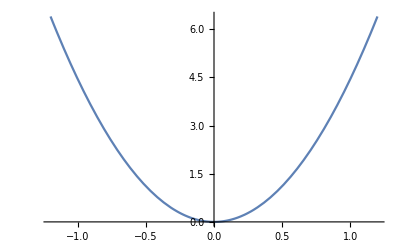

```mathematica
Plot[√2 π x^2,{x,-1.2,1.2}]
```

```mathematica
With[{x=Function[t,t],y=Function[t,t]},
{2π Integrate[(x[t] √(x'[t]^2+y'[t]^2)),t],2π Integrate[(x[t] √(x'[t]^2+y'[t]^2)),t]}
]
```

{√2 π t^2,√2 π t^2}

```mathematica
(ⅇ^(-x^2/2))/(√(2 π))
```

```mathematica
PDF[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ],{x,y}]
```

(ⅇ^(-((x-μ_1)^2/σ_1^2+(y-μ_2)^2/σ_2^2-(2 ρ (x-μ_1) (y-μ_2))/(σ_1 σ_2))/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
PDF[BinormalDistribution[{0,0},{1,1},ρ],{x,y}]
```

(ⅇ^(-(x^2+y^2-2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1-ρ^2))

```mathematica
PDF[BinormalDistribution[{0,0},{1,1},1],{x,y}]
```

PDF[BinormalDistribution[{0,0},{1,1},1],{x,y}]

```mathematica
PDF[BinormalDistribution[{Subscript[σ, 1],Subscript[σ, 2]},ρ],{x,y}]
```

(ⅇ^(-(x^2/σ_1^2+y^2/σ_2^2-(2 x y ρ)/(σ_1 σ_2))/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
PDF[BinormalDistribution[ρ],{x,y}]
```

(ⅇ^(-(x^2+y^2-2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1-ρ^2))

```mathematica
PDF[BinormalDistribution[0],{x,y}]
```

(ⅇ^(1/2 (-x^2-y^2)))/(2 π)

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(2 π),{x,-0.4390705798433546,0.43907057708527997},{y,-0.43907057708698427,0.4390705798416503}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(2 π),{x,-0.4390705798433546,0.43907057708527997},{x,y}∈Disk[]]
```

Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(2 π),{x,-0.439071,0.439071},{x,y}∈Disk[]]

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(2 π),{x,-4,4},{y,-4,4},PlotRange->Full]
```

-Graphics3D-

```mathematica
(ⅇ^(1/2 (-x^2-y^2)))/(2 π)
```

(ⅇ^(1/2 (-x^2-y^2)))/(2 π)

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==(ⅇ^(-x^2/2))/(√(2 π))},u[x,t],{x,t}]
```

{{u[x,t]→(ⅇ^(-x^2/(2+4 t)))/(√(2 π) √(1+2 t))}}

```mathematica
Plot3D[
(ⅇ^(-x^2/(2+4 t)))/(√(2 π) √(1+2 t)),
{x,-2,2},{t,0,5},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[
(ⅇ^(-x^2/(2+4 t)))/(√(2 π) √(1+2 t)),
{x,-2,2},{t,0,50},PlotRange->Full]
```

-Graphics3D-

```mathematica
Integrate[(ⅇ^(-x^2/(2+4 t)))/(√(2 π) √(1+2 t)),{x,-2,2}]
```

Erf[2/(√(2+4 t))]

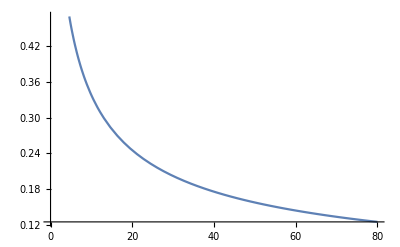

```mathematica
Plot[Erf[2/(√(2+4 t))],{t,0,80}]
```

```mathematica
FullSimplify[Erf[2/(√(2+4 t))]]
```

Erf[1/(√(1/2+t))]

```mathematica
Limit[Erf[2/(√(2+4 t))],t->∞]
```

0

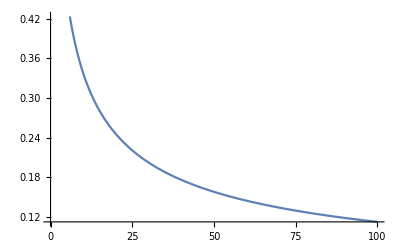

```mathematica
Plot[Erf[2/(√(2+4 t))],{t,0,100}]
```

```mathematica
Manipulate[
Plot[
Erf[2/(√(2+4 t))]
,{t,0,100}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[
(ⅇ^(-x^2/(2+4 (100 a))))/(√(2 π) √(1+2 (100 a)))
,{x,-2,2},PlotRange->{0,1}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[
(1-a)(ⅇ^(-x^2/2))/(√(2 π))
,{x,-2,2},PlotRange->{0,1}]
,{a,0,1}]
```

```mathematica
Integrate[(ⅇ^(-x^2/(2+4 t)))/(√(2 π) √(1+2 t)),x]
```

(√(1/2+t) Erf[x/(√(2+4 t))])/(√2 √(1+2 t))

```mathematica
Plot3D[(√(1/2+t) Erf[x/(√(2+4 t))])/(√2 √(1+2 t)),{t,0,8},{x,-30,30}]
```

-Graphics3D-

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==f[x]},u[x,t],{x,t}]
```

{{u[x,t]→Integrate[(ⅇ^(-(x-K[1])^2/(4 t)) f[K[1]])/(2 √π √t),{K[1],-∞,∞},Assumptions→t>0]}}

```mathematica
f[x]+g[x]==h[x]
```

f[x]+g[x]==h[x]

```mathematica
(1-a[x])f[x]+a[x]g[x]==h[x]
```

(1-a[x]) f[x]+a[x] g[x]==h[x]

```mathematica
FullSimplify[(1-a[x]) f[x]+a[x] g[x]==h[x],{x,a[x],f[x],g[x]}∈Reals∧0≤a[x]≤1]
```

(-1+a[x]) f[x]+h[x]==a[x] g[x]

```mathematica
Reduce[(-1+a[x]) f[x]+h[x]==a[x] g[x]]
```

(g[x]==h[x]&&f[x]==h[x])||(-f[x]+g[x]≠0&&a[x]==(f[x]-h[x])/(f[x]-g[x]))

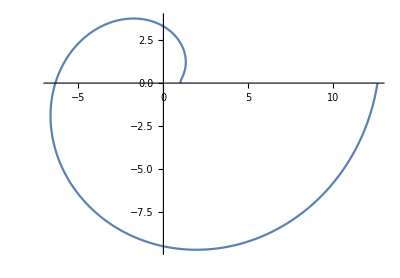

```mathematica
PolarPlot[√(1+4 θ^2),{θ,0,2π}]
```

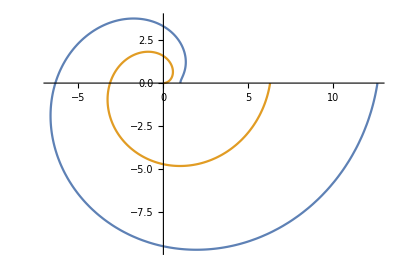

```mathematica
PolarPlot[
{√(1+4 θ^2),θ}
,{θ,0,2π}]
```

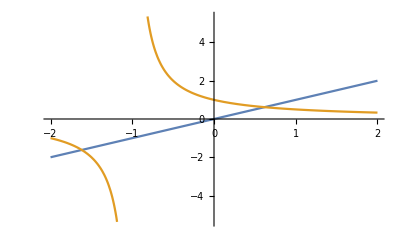

```mathematica
Plot[
{x,1/(1+x)}
,{x,-2,2}]
```

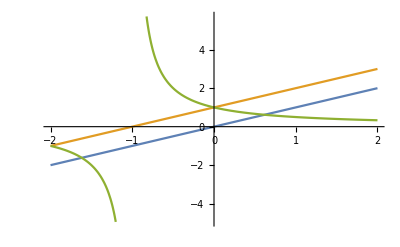

```mathematica
Plot[
{x,1+x,1/(1+x)}
,{x,-2,2}]
```

```mathematica
Manipulate[
Plot[
{x,1/(1+x),(1-a)x+a/(1+x)},
{x,-3,3}],
{a,0,1}]
```

```mathematica
Plot3D[
(1-a)x+a/(1+x)
,{x,-3,3},Subscript[ℵ, a],PlotRange->Full]
```

-Graphics3D-

```mathematica
x==1/(1+x)==(1-a)x+a/(1+x)
```

x==1/(1+x)==(1-a) x+a/(1+x)

```mathematica
Reduce[x==1/(1+x)==(1-a) x+a/(1+x)]
```

x==1/2 (-1-√5)||x==1/2 (-1+√5)

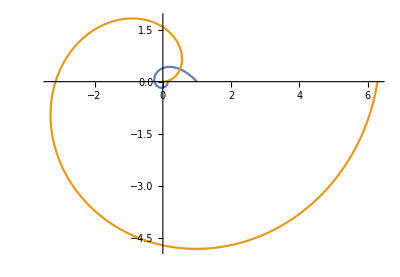

```mathematica
PolarPlot[
{1/(1+θ),θ}
,{θ,0,2π}]
```

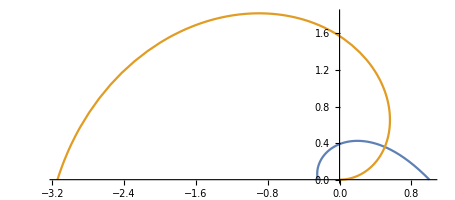

```mathematica
PolarPlot[
{1/(1+θ),θ}
,{θ,0,π}]
```